# Lists Part 1

## Basic Exercises

### Question Subsection

Generate a list from 1 to 10 using the Range function.

#### Solution

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

### Question Subsection

Generate a list from 10 to 20.

#### Solution

```mathematica
Range[10,20]
```

{10,11,12,13,14,15,16,17,18,19,20}

### Question Subsection

Generate a list from 100 down to 1.

#### Solution

```mathematica
Range[100,1,-1]
```

{100,99,98,97,96,95,94,93,92,91,90,89,88,87,86,85,84,83,82,81,80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,55,54,53,52,51,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

### Question Subsection

Generate a list of all even numbers from 2 to 50.

#### Solution

```mathematica
Range[2,50,2]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50}

### Question Subsection

Use the Length function to find the length of the following list:

```mathematica
{2,4,6,1,2,3}
```

#### Solution

```mathematica
Length@{2,4,6,1,2,3}
```

6

```mathematica
(* or *)
```

```mathematica
Length[{2,4,6,1,2,3}]
```

6

### Question Subsection

Use the Depth function to find the depth of:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

#### Solution

```mathematica
Depth[Range[10]]
```

2

### Question Subsection

Use the Depth function to find the depth of:

```mathematica
Table[{i,j},{i,5},{j,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}},{{5,1},{5,2},{5,3},{5,4}}}

#### Solution

```mathematica
Depth[Table[{i,j},{i,5},{j,4}]]
```

```mathematica
Depth[%]
```

4

```mathematica
(* the depth can also be seen clearly using TreeForm function *)
```

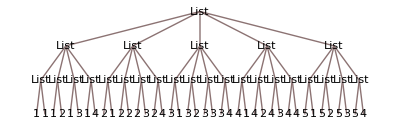

```mathematica
TreeForm[Table[{i,j},{i,5},{j,4}]]
```

### Question Subsection

Use the Table function to generate the values 1 through 10 (like Range[10]).

#### Solution

```mathematica
Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

### Question Subsection

Use the Flatten function to generate the values 1 through 10 twice, i.e. {1, 2, ..., 10, 1, 2, ... 10}.

#### Solution

```mathematica
Flatten[{Range[10],Range[10]}]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10}

### Question Subsection

Use the Flatten and Table functions to generate all pairs of values {1, 1} to {3, 3}.

#### Solution

```mathematica
Flatten[Table[{i,j},{i,3},{j,3}],1]
```

### Question Subsection

Use Partition to group the values 1 through 100 in groups of 5.

#### Solution

```mathematica
Partition[Range[100],5]//MatrixForm
```

(1 | 2 | 3 | 4 | 5
6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15
16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25
26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35
36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45
46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55
56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65
66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75
76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85
86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95
96 | 97 | 98 | 99 | 100)

### Question Subsection

The Prime function generates the nth prime:

Prime[n] gives the n^th prime number.

Use the Table function to generate the first 50 prime numbers.

#### Solution

```mathematica
Table[Prime[i],{i,50}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229}

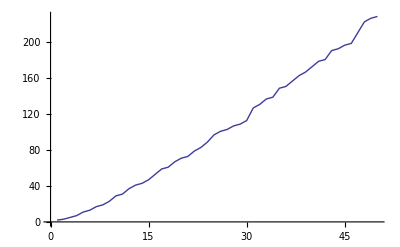

```mathematica
ListLinePlot[%]
```

### Question Subsection

Given:

```mathematica
primes=Prime[Range[50]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229}

Use the Part function to get the 25th prime number.

#### Solution

```mathematica
primes[[50]]
```

```mathematica
Part[primes, 50]
```

229

```mathematica
(* or using shorthand *)
```

```mathematica
primes[[50]]
```

229

### Question Subsection

Given the conditions from Question Subsection use Part and Span to get the 10th through 20th prime numbers.

#### Solution

```mathematica
?Span
```

i;;j represents a span of elements i through j.
i;; represents a span from i to the end.
;;j represents a span from the beginning to j.
;; represents a span that includes all elements.
i;;j;;k represents a span from i through j in steps of k.
i;;;;k represents a span from i to the end in steps of k.
;;j;;k represents a span from the beginning to j in steps of k.
;;;;k represents a span from the beginning to the end in steps of k.

```mathematica
primes[[10;;20]]
```

```mathematica
Part[primes, Span[10,20]]
```

{29,31,37,41,43,47,53,59,61,67,71}

### Question Subsection

Given the conditions from Question Subsection use Take to get the 10th through 20th prime numbers.

```mathematica
?Take
```

Take[list,n] gives the first n elements of list. 
Take[list,-n] gives the last n elements of list. 
Take[list,{m,n}] gives elements m through n of list. 
Take[list,seq_1,seq_2,…] gives a nested list in which elements specified by seq_i are taken at level i in list.

#### Solution

```mathematica
Take[primes,{10,20}]
```

```mathematica
Take[primes,{10,20}]
```

{29,31,37,41,43,47,53,59,61,67,71}

## Advanced Exercises

You will need the following variables defined in order to do the exercises in this section. Please evaluate these cells before you continue.

```mathematica
deck=Tuples[{{2,3,4,5,6,7,8,9,10,J,Q,K,A},{♢,♣,♡,♠}}]
```

{{2,♢},{2,♣},{2,♡},{2,♠},{3,♢},{3,♣},{3,♡},{3,♠},{4,♢},{4,♣},{4,♡},{4,♠},{5,♢},{5,♣},{5,♡},{5,♠},{6,♢},{6,♣},{6,♡},{6,♠},{7,♢},{7,♣},{7,♡},{7,♠},{8,♢},{8,♣},{8,♡},{8,♠},{9,♢},{9,♣},{9,♡},{9,♠},{10,♢},{10,♣},{10,♡},{10,♠},{J,♢},{J,♣},{J,♡},{J,♠},{Q,♢},{Q,♣},{Q,♡},{Q,♠},{K,♢},{K,♣},{K,♡},{K,♠},{A,♢},{A,♣},{A,♡},{A,♠}}

### Question Subsection

Get the all kings from the deck.

#### Hint

The King starts at position 45,

#### Solution

```mathematica
deck[[45;;48]]
```

{{K,♢},{K,♣},{K,♡},{K,♠}}

```mathematica
(* or; (i) group the cards in ascending order and (ii) select the second highest value row...this way makes more sense  *)
```

```mathematica
Partition[deck,4][[-2]]
```

{{K,♢},{K,♣},{K,♡},{K,♠}}

### Question Subsection

Get all the hearts from the deck.

#### Hint

Use the 6th form of part:

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.
expr[[key]] gives the value associated with the key "key" in an association expr.
expr[[Key[k]]] gives the value associated with an arbitrary key k in the association expr.

#### Solution

```mathematica
deck[[3;;-1;;4]]
```

{{2,♡},{3,♡},{4,♡},{5,♡},{6,♡},{7,♡},{8,♡},{9,♡},{10,♡},{J,♡},{Q,♡},{K,♡},{A,♡}}

```mathematica
(* or (i) group the cards in ascending order and (ii) select all rows with hearts i.e. column 3*)
```

```mathematica
Partition[deck,4][[All,3]]
```

{{2,♡},{3,♡},{4,♡},{5,♡},{6,♡},{7,♡},{8,♡},{9,♡},{10,♡},{J,♡},{Q,♡},{K,♡},{A,♡}}

### Question Subsection

Get all the diamonds and hearts from the deck.

#### Hint

Use Flatten with two sets of Part specifications.

#### Solution

```mathematica
Flatten[{deck[[1;;-1;;4]],deck[[3;;-1;;4]]},1]
```

{{2,♢},{3,♢},{4,♢},{5,♢},{6,♢},{7,♢},{8,♢},{9,♢},{10,♢},{J,♢},{Q,♢},{K,♢},{A,♢},{2,♡},{3,♡},{4,♡},{5,♡},{6,♡},{7,♡},{8,♡},{9,♡},{10,♡},{J,♡},{Q,♡},{K,♡},{A,♡}}

```mathematica
(* This is more readable *)
```

```mathematica
Flatten[Partition[deck,4][[All,{1,3}]],1]
```

{{2,♢},{2,♡},{3,♢},{3,♡},{4,♢},{4,♡},{5,♢},{5,♡},{6,♢},{6,♡},{7,♢},{7,♡},{8,♢},{8,♡},{9,♢},{9,♡},{10,♢},{10,♡},{J,♢},{J,♡},{Q,♢},{Q,♡},{K,♢},{K,♡},{A,♢},{A,♡}}